## Learning Tests

```mathematica
test2=equ*m0sq*mqd*HoldForm[NIntegrate][E^(-(s/Msq)),{s,0,s0}]/(f3^2*m3^8)
```

This does not work

```mathematica
ReleaseHold[test2]/.{s0->2,Msq->1,f3->1,m3->1}
```

This works

```mathematica
ReleaseHold[test2 /.{s0->2,Msq->1,f3->1,m3->1}]
```

```mathematica
ff[equ_,m0sq_,mqd_,s0_]:=test2 /.{Msq->1,f3->1,m3->1}
ff[equ,m0sq,mqd,s000]
```

```mathematica
ff[equ_,m0sq_,mqd_,s0_]:>test2 /.{Msq->1,f3->1,m3->1}
ff[equ,m0sq,mqd,s000]
```

In order this to work

```mathematica
ff[equ_,m0sq_,mqd_,s0_]=test2 /.{Msq->1,f3->1,m3->1}
ff[equ,m0sq,mqd,s000]
```

```mathematica
ff @@{1,4,9,16}
```

```mathematica
ff @@{1,4,9,16} //ReleaseHold
```

```mathematica
ReleaseHold[ff @@{1,4,9,16} ]
```

```mathematica
ff @@{1,4,9,16}//ReleaseHold
```

Try this in table

```mathematica
?Table
```

```mathematica
t1=Table[i^2,{i,1,4}]
```

```mathematica
ReleaseHold[ff@@t1]
```

```mathematica
Table[ff@]
```

## Error Analysis

Prepared with the help of chatgpt: 
See https://chatgpt.com/share/66fe55e3-ecd0-8007-9d39-ae15c09faa08 
for the chat

```mathematica
(*Set Directoy to the one notebook is running*)
SetDirectory[NotebookDirectory[]]
```

-Graphics-

-Graphics-

```mathematica
f[M_,m_]:= g (M-m)/(M+m)
```

```mathematica
AroundReplace[f[M,m],{
m->Around[50,1],
M->Around[100,1],
g->9.80
} ]//ScientificForm
```

You should try the above procedure. The below method may cause issues for terms m^2 etc. Find an example to test this...

```mathematica
m=Around[50,1]
M=Around[100,1]
g=9.80
f[M,m]
```

```mathematica
(*Define the function*)
f[M_,m_]:=9.80 (M-m)/(M+m) 
(*Parameters with uncertainty*)
mMean=50;
mUncertainty=1;
MMean=100;
MUncertainty=1;

(*Generate 100 random samples from normal distributions for m and M*)
randomSamples=Table[{RandomVariate[NormalDistribution[MMean,MUncertainty]],RandomVariate[NormalDistribution[mMean,mUncertainty]]},{100}];

(*Compute the function for each random pair*)
functionValues=f@@@randomSamples;

(*Plot a histogram of the function values*)
Histogram[functionValues,20,"PDF",PlotRange->All]
```

```mathematica
(*Define the function f with Around for uncertainties*)
f[M_,m_]:=g (M-m)/(M+m)

(*Use Around to include uncertainties in M and m*)
f[Around[100,1],Around[50,1]]
```

```mathematica
g=9.80
```

```mathematica
(*Define the function f[M,m]*)
f[M_,m_]:= g (M-m)/(M+m)
(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Calculate the mean and standard deviation of the results*)
meanValue=Mean[results];
stdDev=StandardDeviation[results];

(*Plot the histogram of the results*)histogram=Histogram[results,50,"PDF",PlotLabel->"Distribution of f(M,m) Values",AxesLabel->{"f(M,m)","Probability"}]

(*Display the mean,standard deviation,and the histogram*)
{meanValue,stdDev,histogram}
```

```mathematica
(*Define the function f[M,m]*)
f[M_,m_]:=g (M-m)/(M+m)

(*Set the number of iterations*)
iterations=500;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];

(*Plot the histogram with a Gaussian fit overlay*)
histogram=Show[Histogram[results,10,"PDF",PlotLabel->"Gaussian Fit to f(M,m) Values",AxesLabel->{"f(M,m)","Probability"}],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->Red]];

(*Display the fitted parameters and the histogram*)
{fit,histogram}
```

```mathematica
(*Define the function f[M,m]*)
f[M_,m_]:=g (M-m)/(M+m)

(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];

(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)
histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to f(M,m) Values",Bold,16],AxesLabel->{Style["f(M,m)",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];

{fit,histogram}

(*Export the plot to a PDF file*)
Export["GaussianFit_Histogram.pdf",histogramPlot,"PDF"]
```

In general this can be written like the follwoing.

```mathematica
(*Define a general Monte Carlo function with uncertainty propagation*)MonteCarloUncertaintyPropagation[f_,params_List,iterations_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{randomParams,results,fit,histogramPlot},
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,params}];
(*Calculate the function for each set of random parameters*)
results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)
Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*)
{fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with uncertainties as {value,uncertainty}*)
params={{100,1},{50,1}}; (*M=100±1,m=50±1*)

(*Call the general Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,100,"GeneralHistogramFit.pdf"]
```

## Generic Function

```mathematica
(*Define a general Monte Carlo function with uncertainty propagation*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with names,values,and uncertainties using an Association*)
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;

(*Call the general Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,100,"GeneralHistogramFit.pdf"]
```

THIS IS FINAL FORM: USE THIS ONE:

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},
(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)
results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)
Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)
g=9.80;
(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with names,values,and uncertainties using an Association*)
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;

(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
```

## Makale Analiz

### Referans

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### Numeric Analysis

```mathematica
(*charge[eta,u]->1/Sqrt[6],charge[eta,d]->1/Sqrt[6],charge[eta,s]->-2/Sqrt[6],charge[pi,u]->1/Sqrt[2],charge[pi,d]->-1/Sqrt[2],eqd->-1/3,eqs->-1/3,equ->2/3,eqc->2/3,eqb->-1/3,mqs->(0.093)*(1.35),mqu->2.2 10^(-3),mqd->4.7 10^(-3),(*bunlar pole mass olarak duzeltilmis halleri*)mqc->1.28,mqb->4.18,m0->Sqrt[0.8],ss->-0.8 (0.24)^3,dd->-(0.24)^3,uu->-(0.24)^3,xi->-3.15,f3gamma->-0.0039,lam->0.5,(*lam ve LMB ayni*)LMB->0.5,(**)gssqGG->4 Pi^2 0.012,gssq->4 Pi 0.32,*)
```

```mathematica
(*eqd=-1/3;
eqs=-1/3;
equ=2/3;
eqc=2/3;
eqb=-1/3;
u0=1/2;
u=1/2;
v=1/2;
zero=0;
*)
constantrules={
eqd->-1/3,
eqs->-1/3,
equ->2/3,
eqc->2/3,
eqb->-1/3,
u0->1/2,
u->1/2,
v->1/2,
zero->0,
EulerGamma->2};
```

```mathematica
params=<|
"mqs"->{0.093*1.35,0.0},
"mqu"->{2.2*10^(-3),0.0},
"mqd"->{4.7*10^(-3),0.0},
"mqc"->{1.28,0.0},
"mqb"->{4.18,0.0},
(*"m0"->{Sqrt[0.8],0.0},*)
"m0sq"->{0.8,0.0},
"dd"->{-(0.246)^3,0.028^3},
"uu"->{-(0.246)^3,0.028^3},
"ss"->{-0.8*(0.246)^3,0.80*0.028^3},
"xi"->{-3.15,0.30},
"f3gamma"->{-0.0039,0},
"lam"->{0.5,0.0},
"LMB"->{0.5,0.0},
"gssqGG"->{4*Pi^2*0.012,0.0},
"gssq"->{4*Pi*0.32,0.0},
"Msq"-> {4.0,1.0},
"s0"->{5.25,0.25},
"m3"->{1.76,0.01},
"f3"->{1.17*10^-2,0.01*10^-2}
|>
```

<|mqs→{0.12555,0.},mqu→{0.0022,0.},mqd→{0.0047,0.},mqc→{1.28,0.},mqb→{4.18,0.},m0sq→{0.8,0.},dd→{-0.0148869,0.000021952},uu→{-0.0148869,0.000021952},ss→{-0.0119095,0.0000175616},xi→{-3.15,0.3},f3gamma→{-0.0039,0},lam→{0.5,0.},LMB→{0.5,0.},gssqGG→{0.473741,0.},gssq→{4.02124,0.},Msq→{4.,1.},s0→{5.25,0.25},m3→{1.76,0.01},f3→{0.0117,0.0001}|>

```mathematica
(*f[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,Msq_,s0_,m3_,f3_]=<<pi_rho3pl_gm53_spin3_monte_carlo_input //.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]//.ninteg->NIntegrate//.nintegrate->NIntegrate*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sbilmis/physics_scripts

```mathematica
fa[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,gssq_,Msq_,s0_,m3_,f3_]=<<pi_rho3pl_gm53_spin3_monte_carlo_input
```

```mathematica
fb[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,gssq_,Msq_,s0_,m3_,f3_]=fa[mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,gssq,Msq,s0,m3,f3]//.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]//.ninteg->HoldForm[NIntegrate]//.nintegrate->HoldForm[NIntegrate] ;
```

```mathematica
fc[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,gssq_,Msq_,s0_,m3_,f3_]:=fb[mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,gssq,Msq,s0,m3,f3]//.constantrules
```

```mathematica
fc[mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,gssq,Msq,s0,m3,f3]//InputForm;
```

```mathematica
params
```

<|mqs→{0.12555,0.},mqu→{0.0022,0.},mqd→{0.0047,0.},mqc→{1.28,0.},mqb→{4.18,0.},m0sq→{0.8,0.},dd→{-0.0148869,0.000021952},uu→{-0.0148869,0.000021952},ss→{-0.0119095,0.0000175616},xi→{-3.15,0.3},f3gamma→{-0.0039,0},lam→{0.5,0.},LMB→{0.5,0.},gssqGG→{0.473741,0.},gssq→{4.02124,0.},Msq→{4.,1.},s0→{5.25,0.25},m3→{1.76,0.01},f3→{0.0117,0.0001}|>

```mathematica
params[[1]]
```

{0.12555,0.}

```mathematica
params[[2]]
```

{0.0022,0.}

```mathematica
paramNames=Keys[params]
paramRanges=Values[params]
```

{mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,gssq,Msq,s0,m3,f3}

(0.12555 | 0.
0.0022 | 0.
0.0047 | 0.
1.28 | 0.
4.18 | 0.
0.8 | 0.
-0.0148869 | 0.000021952
-0.0148869 | 0.000021952
-0.0119095 | 0.0000175616
-3.15 | 0.3
-0.0039 | 0
0.5 | 0.
0.5 | 0.
0.473741 | 0.
4.02124 | 0.
4. | 1.
5.25 | 0.25
1.76 | 0.01
0.0117 | 0.0001)

```mathematica
{param[[1]]-param[[2]],param[[1]]+param[[2]]}
```

Part::partd: Part specification param⟦1⟧ is longer than depth of object.

Part::partd: Part specification param⟦2⟧ is longer than depth of object.

Part::partd: Part specification param⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{param⟦1⟧-param⟦2⟧,param⟦1⟧+param⟦2⟧}

```mathematica
?Table
```

```mathematica
Table[i,{i,3,4}]
Table[i,{i,4}]
```

{3,4}

{1,2,3,4}

```mathematica
paramRanges
```

(0.12555 | 0.
0.0022 | 0.
0.0047 | 0.
1.28 | 0.
4.18 | 0.
0.8 | 0.
-0.0148869 | 0.000021952
-0.0148869 | 0.000021952
-0.0119095 | 0.0000175616
-3.15 | 0.3
-0.0039 | 0
0.5 | 0.
0.5 | 0.
0.473741 | 0.
4.02124 | 0.
4. | 1.
5.25 | 0.25
1.76 | 0.01
0.0117 | 0.0001)

```mathematica
randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},5],{param,paramRanges}]
```

(0.12555 | 0.12555 | 0.12555 | 0.12555 | 0.12555
0.0022 | 0.0022 | 0.0022 | 0.0022 | 0.0022
0.0047 | 0.0047 | 0.0047 | 0.0047 | 0.0047
1.28 | 1.28 | 1.28 | 1.28 | 1.28
4.18 | 4.18 | 4.18 | 4.18 | 4.18
0.8 | 0.8 | 0.8 | 0.8 | 0.8
-0.0148952 | -0.0148996 | -0.0148911 | -0.0148746 | -0.0149
-0.014881 | -0.0148779 | -0.0148799 | -0.014871 | -0.014879
-0.0119268 | -0.011903 | -0.0119155 | -0.011924 | -0.0119108
-3.3712 | -3.20169 | -3.08463 | -3.19553 | -3.39115
-0.0039 | -0.0039 | -0.0039 | -0.0039 | -0.0039
0.5 | 0.5 | 0.5 | 0.5 | 0.5
0.5 | 0.5 | 0.5 | 0.5 | 0.5
0.473741 | 0.473741 | 0.473741 | 0.473741 | 0.473741
4.02124 | 4.02124 | 4.02124 | 4.02124 | 4.02124
4.28843 | 3.46325 | 3.74396 | 3.56485 | 3.22838
5.33839 | 5.13362 | 5.46269 | 5.11404 | 5.31553
1.75991 | 1.75892 | 1.76947 | 1.75337 | 1.75441
0.0116146 | 0.0117838 | 0.0117535 | 0.0116542 | 0.0117716)

```mathematica
results=Table[Re[ReleaseHold[fc @@(randomParams[[All,i]])]],{i,2}]
results2=Table[Chop[ReleaseHold[fc @@(randomParams[[All,i]])]],{i,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.0341719}. NIntegrate obtained 2.46331×10^-16 and 2.00266×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.542961}. NIntegrate obtained -2.28983×10^-16 and 1.18252×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.49999999103240892009249998865812322172003101528048318868968635798}. NIntegrate obtained -6.8695×10^-16 and 6.52431×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{5.64418,6.9966}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.0341719}. NIntegrate obtained 2.46331×10^-16 and 2.00266×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.542961}. NIntegrate obtained -2.28983×10^-16 and 1.18252×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.49999999103240892009249998865812322172003101528048318868968635798}. NIntegrate obtained -6.8695×10^-16 and 6.52431×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{5.64418,6.9966}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.0341719}. NIntegrate obtained 2.46331×10^-16 and 2.00266×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.542961}. NIntegrate obtained -2.28983×10^-16 and 1.18252×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in up near {up} = {0.49999999103240892009249998865812322172003101528048318868968635798}. NIntegrate obtained -6.8695×10^-16 and 6.52431×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

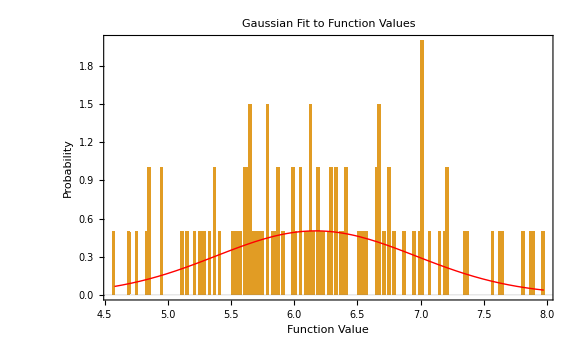
{{6.41197,7.01477,7.97622,5.98558,5.63645,7.19769,7.01191,5.79637,5.69409,6.36696,5.41116,6.99571,6.55036,5.26852,6.18707,4.85705,5.20154,6.29789,6.41648,7.8726,5.78524,5.86351,5.6113,4.57707,4.84083,5.36542,7.57818,7.81109,6.23497,7.34319,7.06857,5.32349,6.05504,6.09396,4.75813,6.11779,5.82018,5.66042,5.60458,5.63426,5.7403,6.56986,6.53541,5.90183,7.01505,7.00099,5.56585,5.14913,7.15768,6.29208,6.01022,7.37627,6.95506,6.65886,6.3389,6.19546,5.87941,7.20771,7.62363,6.64752,7.21383,7.643,6.50535,6.13487,5.25439,5.73797,5.36872,5.65152,6.39938,6.6754,6.27853,6.7531,4.94456,6.75607,6.33179,5.29187,4.95375,6.66862,5.5094,5.65305,6.87475,6.05558,5.79305,6.79959,5.71859,5.9984,5.65786,4.68654,5.10616,6.14004,6.67873,6.12227,5.85261,6.12644,6.20032,7.89332,6.70285,4.82893,5.54897,5.52557},{μ→6.17155,σ→0.792611},-Graphics-}

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},
(*Extract parameter names and their uncertainty ranges*)
paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)
results=Table[Chop[ReleaseHold[f @@(randomParams[[All,i]])]],{i,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)
histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];


(*histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];*)
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){results,fit,histogramPlot}]

(*Example usage*)



(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[fc,params,100,100,"CustomHistogramFit.pdf"]
```

## Another Way:

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,params_Association,iterations_:1000,binSize_:20,exportPath_:"Histogram.pdf"]:=Module[{paramNames,paramMeans,paramSigmas,randomParams,results,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,gaussianFitPlot,combinedPlot},(*Extract parameter names*)paramNames=Keys[params];
(*Extract means and sigmas from the params association*)paramMeans=AssociationMap[params[#][[1]]&,paramNames];(*Extract the first element (mean)*)paramSigmas=AssociationMap[params[#][[2]]&,paramNames];(*Extract the second element (sigma)*)(*Generate random parameter sets based on the means and sigmas from associations*)randomParams=Table[Table[RandomReal[{paramMeans[param]-paramSigmas[param],paramMeans[param]+paramSigmas[param]}],{param,paramNames}],{iterations}];
(*Evaluate the function for each set of random parameters and print the output for each iteration*)results=Table[Module[{output=func@@randomParams[[i]]},Print["Iteration ",i,": ",output];(*Print the output*)output],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram of the results using Scientific plot theme*)histogramPlot=Histogram[results,binSize,"PDF",PlotTheme->"Scientific",AxesLabel->{"Function Output","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real Part of Function","Probability Density"},ImageSize->Large];
(*Plot the fitted Gaussian curve*)gaussianFitPlot=Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All];
(*Combine the histogram and the Gaussian fit plot*)combinedPlot=Show[histogramPlot,gaussianFitPlot,PlotLegends->Placed[{"Fitted Gaussian"},Below]];
(*Display the combined plot on the screen*)Print[combinedPlot];
(*Export the plot to a PDF file*)Export[exportPath,combinedPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function with combined means and sigmas*)

(*(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the parameters with both means and uncertainties in one association*)
params=<|"m3"->{2,0.1},"Msq"->{5,0.1},"uu"->{1.1,0.05},"mqd"->{3,0.1},"f3"->{4,0.1}|>;

(*Call the generalized function with custom iterations,bin size,and PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,params,1000,200,"MyHistogram.pdf"]
*)
```

## Tests

```mathematica
(*General function for generating histogram and uncertainty*)GenerateHistogramAndUncertainty[func_,paramsMeans_,paramsSigmas_,iterations_:1000]:=Module[{numParams,randomParams,results,realResults,uncertainty},(*Number of parameters*)numParams=Length[paramsMeans];
(*Generate random parameter sets based on the means and sigmas*)randomParams=Table[Table[RandomReal[{paramsMeans[[j]]-paramsSigmas[[j]],paramsMeans[[j]]+paramsSigmas[[j]]}],{j,numParams}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[Re[func@@randomParams[[i]]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Plot the histogram of the real part of the results*)Histogram[results,20,"PDF",AxesLabel->{"Real(func)","Probability"},PlotLabel->"Histogram of Real Part of Function"];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
(*Return the histogram and the uncertainty*)Print["The uncertainty in the real part of the function is: ",uncertainty];
uncertainty]

(*Example usage of the generalized function*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 I*E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the means and uncertainties for the parameters*)
means={2,5,1.1,3,4}; (*{m3,Msq,uu,mqd,f3}*)
sigmas={0.1,0.1,0.05,0.1,0.1}; (*Corresponding uncertainties*)

(*Call the generalized function*)
GenerateHistogramAndUncertainty[exampleFunc,means,sigmas,1000]
```

```mathematica
(*General function for generating histogram,uncertainty,and fitting a Gaussian*)GenerateHistogramAndUncertaintyWithFit[func_,paramsMeans_,paramsSigmas_,iterations_:1000]:=Module[{numParams,randomParams,results,realResults,uncertainty,fit,fitMean,fitSigma},(*Number of parameters*)numParams=Length[paramsMeans];
(*Generate random parameter sets based on the means and sigmas*)randomParams=Table[Table[RandomReal[{paramsMeans[[j]]-paramsSigmas[[j]],paramsMeans[[j]]+paramsSigmas[[j]]}],{j,numParams}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[Re[func@@randomParams[[i]]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Plot the histogram of the real part of the results*)Histogram[results,20,"PDF",AxesLabel->{"Real(func)","Probability"},PlotLabel->"Histogram of Real Part of Function"];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the means and uncertainties for the parameters*)
means={2,5,1.1,3,4}; (*{m3,Msq,uu,mqd,f3}*)
sigmas={0.1,0.1,0.05,0.1,0.1}; (*Corresponding uncertainties*)

(*Call the generalized function with Gaussian fit*)
GenerateHistogramAndUncertaintyWithFit[exampleFunc,means,sigmas,1000]
```

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,paramsMeans_,paramsSigmas_,iterations_:1000,exportPath_:"Histogram.pdf"]:=Module[{numParams,randomParams,results,realResults,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,plot},(*Number of parameters*)numParams=Length[paramsMeans];
(*Generate random parameter sets based on the means and sigmas*)randomParams=Table[Table[RandomReal[{paramsMeans[[j]]-paramsSigmas[[j]],paramsMeans[[j]]+paramsSigmas[[j]]}],{j,numParams}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[func@@randomParams[[i]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram and the fitted Gaussian function on top*)histogramPlot=Show[Histogram[results,20,"PDF",PlotTheme->"Detailed",AxesLabel->{"Real(func)","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real part of the function","Probability"},ImageSize->Large,PlotLegends->None],Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All,PlotLegends->Placed[{"Fitted Gaussian"},Below],AxesOrigin->{0,0}]];
(*Display the plot on the screen*)Print[histogramPlot];
(*Export the plot to a PDF file*)Export[exportPath,histogramPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the means and uncertainties for the parameters*)
means={2,5,1.1,3,4}; (*{m3,Msq,uu,mqd,f3}*)
sigmas={0.1,0.1,0.05,0.1,0.1}; (*Corresponding uncertainties*)

(*Call the generalized function with PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,means,sigmas,1000,"MyHistogram.pdf"]
```

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,paramsMeans_,paramsSigmas_,iterations_:1000,exportPath_:"Histogram.pdf"]:=Module[{numParams,randomParams,results,realResults,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,gaussianFitPlot,combinedPlot},(*Number of parameters*)numParams=Length[paramsMeans];
(*Generate random parameter sets based on the means and sigmas*)randomParams=Table[Table[RandomReal[{paramsMeans[[j]]-paramsSigmas[[j]],paramsMeans[[j]]+paramsSigmas[[j]]}],{j,numParams}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[func@@randomParams[[i]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram of the results*)histogramPlot=Histogram[results,20,"PDF",PlotTheme->"Detailed",AxesLabel->{"Real(func)","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real part of the function","Probability"},ImageSize->Large];
(*Plot the fitted Gaussian curve*)gaussianFitPlot=Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All];
(*Combine the histogram and the Gaussian fit plot*)combinedPlot=Show[histogramPlot,gaussianFitPlot,PlotLegends->Placed[{"Fitted Gaussian"},Below]];
(*Display the combined plot on the screen*)Print[combinedPlot];
(*Export the plot to a PDF file*)Export[exportPath,combinedPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the means and uncertainties for the parameters*)
means={2,5,1.1,3,4}; (*{m3,Msq,uu,mqd,f3}*)
sigmas={0.1,0.1,0.05,0.1,0.1}; (*Corresponding uncertainties*)

(*Call the generalized function with PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,means,sigmas,1000,"MyHistogram.pdf"]
```

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,paramMeans_Association,paramSigmas_Association,iterations_:1000,exportPath_:"Histogram.pdf"]:=Module[{paramNames,randomParams,results,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,gaussianFitPlot,combinedPlot},(*Extract parameter names from the association keys*)paramNames=Keys[paramMeans];
(*Generate random parameter sets based on the means and sigmas from associations*)randomParams=Table[Table[RandomReal[{paramMeans[param]-paramSigmas[param],paramMeans[param]+paramSigmas[param]}],{param,paramNames}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[func@@randomParams[[i]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram of the results using Scientific plot theme*)histogramPlot=Histogram[results,20,"PDF",PlotTheme->"Scientific",AxesLabel->{"Function Output","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real Part of Function","Probability Density"},ImageSize->Large];
(*Plot the fitted Gaussian curve*)gaussianFitPlot=Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All];
(*Combine the histogram and the Gaussian fit plot*)combinedPlot=Show[histogramPlot,gaussianFitPlot,PlotLegends->Placed[{"Fitted Gaussian"},Below]];
(*Display the combined plot on the screen*)Print[combinedPlot];
(*Export the plot to a PDF file*)Export[exportPath,combinedPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function using associations*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the means and uncertainties using associations*)
paramMeans=<|"m3"->2,"Msq"->5,"uu"->1.1,"mqd"->3,"f3"->4|>;
paramSigmas=<|"m3"->0.1,"Msq"->0.1,"uu"->0.05,"mqd"->0.1,"f3"->0.1|>;

(*Call the generalized function with PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,paramMeans,paramSigmas,1000,"MyHistogram.pdf"]
```

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,params_Association,iterations_:1000,exportPath_:"Histogram.pdf"]:=Module[{paramNames,paramMeans,paramSigmas,randomParams,results,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,gaussianFitPlot,combinedPlot},(*Extract parameter names*)paramNames=Keys[params];
(*Extract means and sigmas from the params association*)paramMeans=AssociationMap[params[#][[1]]&,paramNames];(*Extract the first element (mean)*)paramSigmas=AssociationMap[params[#][[2]]&,paramNames];(*Extract the second element (sigma)*)(*Generate random parameter sets based on the means and sigmas from associations*)randomParams=Table[Table[RandomReal[{paramMeans[param]-paramSigmas[param],paramMeans[param]+paramSigmas[param]}],{param,paramNames}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[Re[func@@randomParams[[i]]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram of the results using Scientific plot theme*)histogramPlot=Histogram[results,20,"PDF",PlotTheme->"Scientific",AxesLabel->{"Function Output","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real Part of Function","Probability Density"},ImageSize->Large];
(*Plot the fitted Gaussian curve*)gaussianFitPlot=Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All];
(*Combine the histogram and the Gaussian fit plot*)combinedPlot=Show[histogramPlot,gaussianFitPlot,PlotLegends->Placed[{"Fitted Gaussian"},Below]];
(*Display the combined plot on the screen*)Print[combinedPlot];
(*Export the plot to a PDF file*)Export[exportPath,combinedPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function with combined means and sigmas*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the parameters with both means and uncertainties in one association*)
params=<|"m3"->{2,0.1},"Msq"->{5,0.1},"uu"->{1.1,0.05},"mqd"->{3,0.1},"f3"->{4,0.1}|>;

(*Call the generalized function with PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,params,1000,"MyHistogram.pdf"]
```

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,params_Association,iterations_:1000,binSize_:20,exportPath_:"Histogram.pdf"]:=Module[{paramNames,paramMeans,paramSigmas,randomParams,results,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,gaussianFitPlot,combinedPlot},(*Extract parameter names*)paramNames=Keys[params];
(*Extract means and sigmas from the params association*)paramMeans=AssociationMap[params[#][[1]]&,paramNames];(*Extract the first element (mean)*)paramSigmas=AssociationMap[params[#][[2]]&,paramNames];(*Extract the second element (sigma)*)(*Generate random parameter sets based on the means and sigmas from associations*)randomParams=Table[Table[RandomReal[{paramMeans[param]-paramSigmas[param],paramMeans[param]+paramSigmas[param]}],{param,paramNames}],{iterations}];
(*Evaluate the function for each set of random parameters*)results=Table[Re[func@@randomParams[[i]]],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram of the results using Scientific plot theme*)histogramPlot=Histogram[results,binSize,"PDF",PlotTheme->"Scientific",AxesLabel->{"Function Output","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real Part of Function","Probability Density"},ImageSize->Large];
(*Plot the fitted Gaussian curve*)gaussianFitPlot=Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All];
(*Combine the histogram and the Gaussian fit plot*)combinedPlot=Show[histogramPlot,gaussianFitPlot,PlotLegends->Placed[{"Fitted Gaussian"},Below]];
(*Display the combined plot on the screen*)Print[combinedPlot];
(*Export the plot to a PDF file*)Export[exportPath,combinedPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function with combined means and sigmas*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the parameters with both means and uncertainties in one association*)
params=<|"m3"->{2,0.1},"Msq"->{5,0.1},"uu"->{1.1,0.05},"mqd"->{3,0.1},"f3"->{4,0.1}|>;

(*Call the generalized function with custom iterations,bin size,and PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,params,2000,30,"MyHistogram.pdf"]
```

```mathematica
(*General function for generating histogram,uncertainty,Gaussian fit,and exporting PDF*)GenerateHistogramAndUncertaintyWithFitExport[func_,params_Association,iterations_:1000,binSize_:20,exportPath_:"Histogram.pdf"]:=Module[{paramNames,paramMeans,paramSigmas,randomParams,results,uncertainty,fit,fitMean,fitSigma,pdfFit,histogramPlot,gaussianFitPlot,combinedPlot},(*Extract parameter names*)paramNames=Keys[params];
(*Extract means and sigmas from the params association*)paramMeans=AssociationMap[params[#][[1]]&,paramNames];(*Extract the first element (mean)*)paramSigmas=AssociationMap[params[#][[2]]&,paramNames];(*Extract the second element (sigma)*)(*Generate random parameter sets based on the means and sigmas from associations*)randomParams=Table[Table[RandomReal[{paramMeans[param]-paramSigmas[param],paramMeans[param]+paramSigmas[param]}],{param,paramNames}],{iterations}];
(*Evaluate the function for each set of random parameters and print the output for each iteration*)results=Table[Module[{output=func@@randomParams[[i]]},Print["Iteration ",i,": ",output];(*Print the output*)output],(*Apply func to each set of parameters and get the real part*){i,iterations}];
(*Calculate the uncertainty (standard deviation) of the real part*)uncertainty=StandardDeviation[results];
meanResult=Mean[results];
(*Fit a Gaussian distribution to the results*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
fitMean=μ/. fit;
fitSigma=σ/. fit;
(*Create the fitted Gaussian function*)pdfFit[x_]:=PDF[NormalDistribution[fitMean,fitSigma],x];
(*Plot the histogram of the results using Scientific plot theme*)histogramPlot=Histogram[results,binSize,"PDF",PlotTheme->"Scientific",AxesLabel->{"Function Output","Probability"},PlotLabel->"Histogram with Fitted Gaussian",Frame->True,FrameLabel->{"Real Part of Function","Probability Density"},ImageSize->Large];
(*Plot the fitted Gaussian curve*)gaussianFitPlot=Plot[Evaluate[pdfFit[x]],{x,Min[results],Max[results]},PlotStyle->{Red,Thick},PlotRange->All];
(*Combine the histogram and the Gaussian fit plot*)combinedPlot=Show[histogramPlot,gaussianFitPlot,PlotLegends->Placed[{"Fitted Gaussian"},Below]];
(*Display the combined plot on the screen*)Print[combinedPlot];
(*Export the plot to a PDF file*)Export[exportPath,combinedPlot,"PDF"];
(*Compare the Monte Carlo mean and uncertainty with the Gaussian fit*)Print["Monte Carlo mean: ",meanResult];
Print["Monte Carlo uncertainty (std dev): ",uncertainty];
Print["Fitted Gaussian mean: ",fitMean];
Print["Fitted Gaussian standard deviation: ",fitSigma];
(*Return the Gaussian fit parameters and the uncertainty*){fitMean,fitSigma,meanResult,uncertainty}]

(*Example usage of the generalized function with combined means and sigmas*)

(*(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the parameters with both means and uncertainties in one association*)
params=<|"m3"->{2,0.1},"Msq"->{5,0.1},"uu"->{1.1,0.05},"mqd"->{3,0.1},"f3"->{4,0.1}|>;

(*Call the generalized function with custom iterations,bin size,and PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,params,1000,200,"MyHistogram.pdf"]
*)
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 *E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Define the parameters with both means and uncertainties in one association*)
params=<|"m3"->{2,0.1},"Msq"->{5,0.1},"uu"->{1.1,0.05},"mqd"->{3,0.1},"f3"->{4,0.1}|>;

(*Call the generalized function with custom iterations,bin size,and PDF export*)
GenerateHistogramAndUncertaintyWithFitExport[exampleFunc,params,1000,200,"MyHistogram.pdf"]
```

```mathematica
(*Example function*)exampleFunc[m3_,Msq_,uu_,mqd_,f3_]:=(13 I*E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)

(*Test with specific values for the parameters*)
testParams={2,5,1.1,3,4}; (*{m3,Msq,uu,mqd,f3}*)

(*Apply the parameters to the function*)
output=exampleFunc@@testParams;

(*Print the result*)
Print["Output for specific test parameters: ",output]
```

```mathematica
(*Another test case with different parameters*)testParams2={1.5,4.8,1.2,2.5,3.8};
output2=exampleFunc@@testParams2;
Print["Output for testParams2: ",output2]
```